```mathematica
allGraphs=allGraphs3; realyNullAtomKeys=allGraphs3NullAtomKeys;
```

## Some definitions first

```mathematica
IsRefinement[sets1_,sets2_]:=Block[{sets,result=False,merged},
sets=Subsets[sets2,{2}];
Table[
merged=Sort[Join[s[[1]],s[[2]]]];
If[MemberQ[sets1,merged],
result=True
(*Print["Not member",merged, " from ",sets1]*)
]
,
{s,sets}];
result
]
```

```mathematica
MobiusGraph[key_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[to[[1]],from[[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Tooltip[Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue]},TableAlignments->Center]),Pi/4],found[n,"graph"]],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
MobiusTable[key_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars,result=Association[],set,level},
vars=ListofVars[form];
Table[
level=StringCount[SymbolName[n],"x"];
If[KeyExistsQ[result,level],
set=result[level],
set={}
];
set=Append[set,Coefficient[form,n]];
result[level]=set
,{n,vars}];
result
]
```

```mathematica
BaseVarComp[v1_,v2_]:=Block[{s1,s2,l1,l2},
s1=SymbolName[v1];
s2=SymbolName[v2];
l1=StringCount[s1,"x"];
l2=StringCount[s2,"x"];
If[l1≠l2,
l1<l2,
s1<s2
]
]
```

## Inequalities so we have pairs

```mathematica
ineqs=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

15

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqs2=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

15

```mathematica
ineqs2
```

{n1x2x3>0,-n12x3+n1x2x3>0,n123-n12x3-n13x2+n1x2x3>0,2 n123-n12x3-n13x2-n1x23+n1x2x3>0,-n123+n1x23>0,-n123+n13x2>0,n123-n12x3-n1x23+n1x2x3>0,n12x3>0,-n123+n12x3>0,n123>0,-n13x2+n1x2x3>0,n123-n13x2-n1x23+n1x2x3>0,n13x2>0,-n1x23+n1x2x3>0,n1x23>0}

```mathematica
realnullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofourrealnull"],0],{k,realyNullAtomKeys}];Length[realnullAtomFacts]
```

5

```mathematica
ineqsW2=Monitor[Simplify[Fold[And,Select[ineqs2,Length[ListofVars[#]]==2&]],Trig->False,ComplexityFunction->MyLeafCount],countDone];Length[ineqsW2]
```

6

```mathematica
Length[allGraphs]
```

15

```mathematica
allGraphs[9,"colofourrealnull"]
```

-n12x3+n1x2x3

```mathematica
vars2=Sort[DeleteDuplicates[ListofVars[Select[ineqsW2,Length[ListofVars[#]]==2&]]],BaseVarComp]
```

{n123,n12x3,n13x2,n1x23,n1x2x3}

```mathematica
InverseNull[symbol_]:=First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==symbol&]]
```

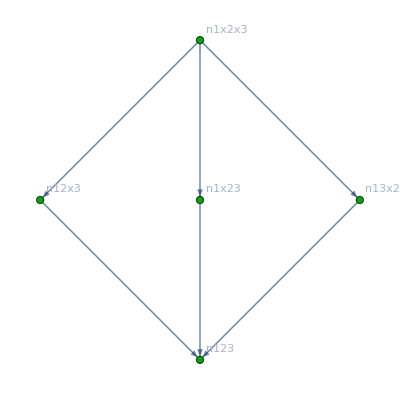

```mathematica
partialOrder=Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[k->Labeled[allGraphs[InverseNull[k],"graph"],k],{k,vars2}],GraphLayout->"LayeredDigraphEmbedding", VertexStyle->Table[k->ColourForKey[allGraphs,InverseNull[k]],{k,vars2}]]
```

```mathematica
EdgeCount[partialOrder]
```

6

```mathematica
VertexCount[partialOrder]
```

5

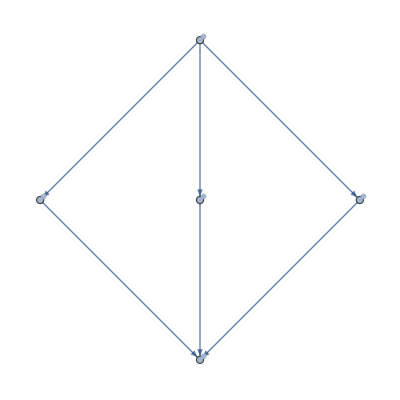

```mathematica
Graph[Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofourrealnull"]->allGraphs[k,"graph"],{k,realyNullAtomKeys}],MemberQ[vars2,#[[1]]]&]]
```

```mathematica
Take[ineqsW,5]
```

Take::normal: Nonatomic expression expected at position 1 in Take[ineqsW,5].

Take[ineqsW,5]

```mathematica
pairs=Subsets[nullAtomSymbols,{2}];Length[pairs]
```

Subsets::normal: Nonatomic expression expected at position 1 in Subsets[nullAtomSymbols,{2}].

2

```mathematica
Take[nullAtomFacts,3]
```

Take::normal: Nonatomic expression expected at position 1 in Take[nullAtomFacts,3].

Take[nullAtomFacts,3]

```mathematica
atomFactsAnd=Fold[And,nullAtomFacts]
```

Fold::normal: Nonatomic expression expected at position 2 in Fold[And,nullAtomFacts].

Fold[And,nullAtomFacts]

```mathematica
allGraphs[6562,"graph"]
```

Missing[KeyAbsent,6562]

## Mobius and zeta

```mathematica
BaseVarComp[v1_,v2_]:=Block[{s1,s2,l1,l2,set1,set2},
s1=StringDrop[SymbolName[v1],1];
s2=StringDrop[ SymbolName[v2],1];
BaseVarComp2[s1,s2]
]
```

```mathematica
BaseVarComp2[v1_,v2_]:=Block[{s1,s2,l1,l2,set1,set2},
s1=v1;
s2=v2;
l1=StringCount[s1,"x"];
l2=StringCount[s2,"x"];
If[l1≠l2,
l1<l2,
set1=FromDigits[ Sort[Map[StringLength[#]&,StringSplit[s1,"x"]],#1<#2&],10];
set2=FromDigits[Sort[Map[StringLength[#]&,StringSplit[s2,"x"]],#1<#2&],10];
If[set1≠set2,
set1<set2,
TrueQ[s1<s2]
]
]
]
```

```mathematica
allVars=Sort[DeleteDuplicates[ListofVars[ineqsW2]]]
```

{n123,n12x3,n13x2,n1x23,n1x2x3}

```mathematica
Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==203&]
```

{}

```mathematica
vertices=Sort[Sort[allVars],BaseVarComp]
```

{n123,n1x23,n13x2,n12x3,n1x2x3}

```mathematica
Length[vertices]
```

5

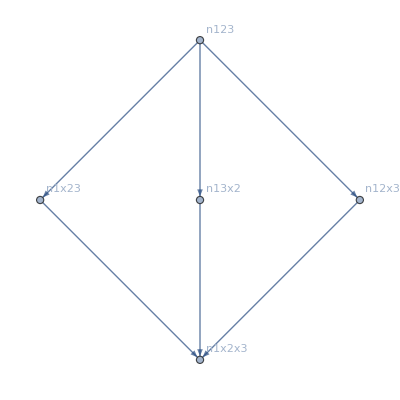

```mathematica
four=Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
IM=IdentityMatrix[Length[VertexList[four]]];
```

```mathematica
fourM=AdjacencyMatrix[four];MatrixForm[fourM]
```

(0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)

```mathematica
MakeOne[mat_]:=Map[Map[If[#!=0,1,0]&,#]&, mat]
```

```mathematica
ZetaM=MakeOne[Inverse[IM-fourM]];MatrixForm[ZetaM]
```

(1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1)

```mathematica
MobiusM=Inverse[ZetaM];MatrixForm[MobiusM,TableHeadings->{VertexList[four],Map[Rotate[#,-Pi/2]&, VertexList[four]]}]
```

( | n123 | n1x23 | n13x2 | n12x3 | n1x2x3
n123 | 1 | -1 | -1 | -1 | 2
n1x23 | 0 | 1 | 0 | 0 | -1
n13x2 | 0 | 0 | 1 | 0 | -1
n12x3 | 0 | 0 | 0 | 1 | -1
n1x2x3 | 0 | 0 | 0 | 0 | 1)

```mathematica
Det[MobiusM]
```

1

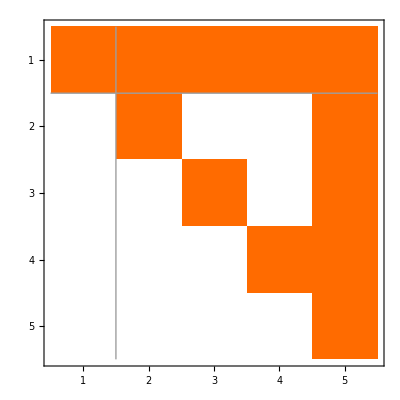

```mathematica
MatrixPlot[ZetaM,Mesh->{Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}],Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}]}]
```

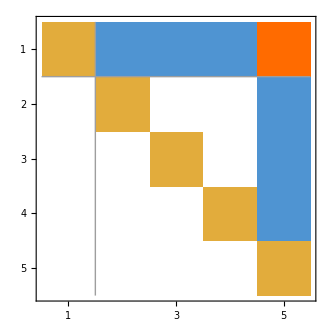

```mathematica
MatrixPlot[MobiusM,Mesh->{Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}],Table[Sum[StirlingS2[6,i],{i,1,k}],{k,1,6}]}]
```

```mathematica
Mob=Association[]
```

<||>

```mathematica
Length[VertexList[four]]
```

5

```mathematica
MobiusM[[5]]
```

{0,0,0,0,1}

```mathematica
With[{l=VertexList[four]},
Table[Mob[l[[k]]]=MobiusM[[Length[l],k]],{k,1,Length[l]}]
]
```

{0,0,0,0,1}

```mathematica
Gr=Association[];With[{l=VertexList[four]},
Table[Gr[l[[k]]]=allGraphs[First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==l[[k]]&]],"vertexsets"],{k,1,Length[l]}]
]
```

{{{1,2,3}},{{1},{2,3}},{{1,3},{2}},{{1,2},{3}},{{1},{2},{3}}}

```mathematica
Gr2=Association[];With[{l=VertexList[four]},
Table[Gr2[l[[k]]]=allGraphs[First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==l[[k]]&]]],{k,1,Length[l]}]
];
```

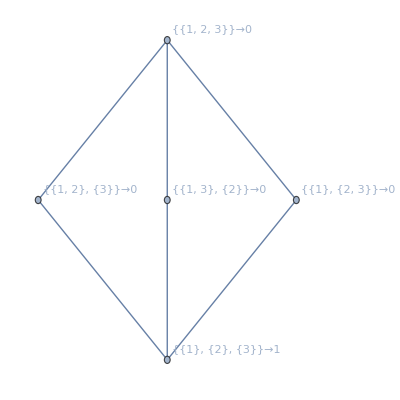

```mathematica
Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->Rotate[ToString[Gr[v]],Pi/4]->Mob[v],{v,VertexList[four]}],GraphLayout->"TutteEmbedding",DirectedEdges->False]
```

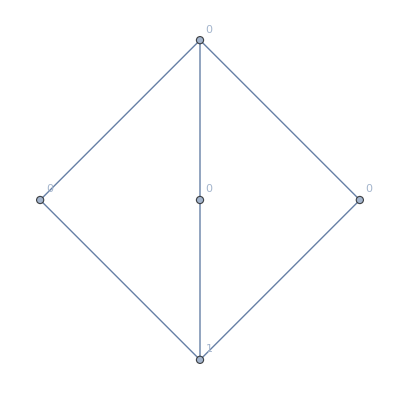

```mathematica
Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->Mob[v],{v,VertexList[four]}],GraphLayout->"TutteEmbedding",DirectedEdges->False]
```

```mathematica
Take[Table[{Gr2[v,"graph"],v,Gr[v],Mob[v],4^Length[Gr[v]],FactorInteger[Mob[v]*4^Length[Gr[v]]]},{v,VertexList[four]}],3]
```

{{-Graphics-,n123,{{1,2,3}},0,4,{{0,1}}},{-Graphics-,n1x23,{{1},{2,3}},0,16,{{0,1}}},{-Graphics-,n13x2,{{1,3},{2}},0,16,{{0,1}}}}

```mathematica
TableForm[Sort[Table[{Gr2[v,"graph"],v,Gr[v],Mob[v],4^Length[Gr[v]],Mob[v]*4^Length[Gr[v]],FactorInteger[Mob[v]*4^Length[Gr[v]]]},{v,VertexList[four]}],Abs[#1[[4]]]>Abs[#2[[4]]]&],TableDepth->2]
```

-Graphics- | n1x2x3 | {{1},{2},{3}} | 1 | 64 | 64 | {{2,6}}
-Graphics- | n12x3 | {{1,2},{3}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n13x2 | {{1,3},{2}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n1x23 | {{1},{2,3}} | 0 | 16 | 0 | {{0,1}}
-Graphics- | n123 | {{1,2,3}} | 0 | 4 | 0 | {{0,1}}

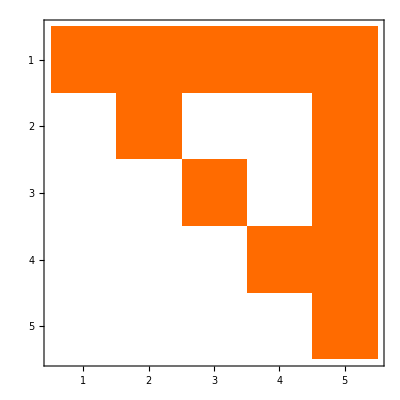

```mathematica
ZetaM//MatrixPlot
```

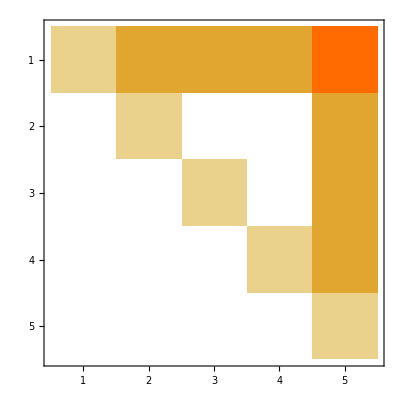

```mathematica
MatrixPower[ZetaM,2]//MatrixPlot
```

```mathematica
Table[MatrixPower[ZetaM,k]//MatrixForm,{k,0,10}]
```

{(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1),(1 | 2 | 2 | 2 | 5
0 | 1 | 0 | 0 | 2
0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 1 | 2
0 | 0 | 0 | 0 | 1),(1 | 3 | 3 | 3 | 12
0 | 1 | 0 | 0 | 3
0 | 0 | 1 | 0 | 3
0 | 0 | 0 | 1 | 3
0 | 0 | 0 | 0 | 1),(1 | 4 | 4 | 4 | 22
0 | 1 | 0 | 0 | 4
0 | 0 | 1 | 0 | 4
0 | 0 | 0 | 1 | 4
0 | 0 | 0 | 0 | 1),(1 | 5 | 5 | 5 | 35
0 | 1 | 0 | 0 | 5
0 | 0 | 1 | 0 | 5
0 | 0 | 0 | 1 | 5
0 | 0 | 0 | 0 | 1),(1 | 6 | 6 | 6 | 51
0 | 1 | 0 | 0 | 6
0 | 0 | 1 | 0 | 6
0 | 0 | 0 | 1 | 6
0 | 0 | 0 | 0 | 1),(1 | 7 | 7 | 7 | 70
0 | 1 | 0 | 0 | 7
0 | 0 | 1 | 0 | 7
0 | 0 | 0 | 1 | 7
0 | 0 | 0 | 0 | 1),(1 | 8 | 8 | 8 | 92
0 | 1 | 0 | 0 | 8
0 | 0 | 1 | 0 | 8
0 | 0 | 0 | 1 | 8
0 | 0 | 0 | 0 | 1),(1 | 9 | 9 | 9 | 117
0 | 1 | 0 | 0 | 9
0 | 0 | 1 | 0 | 9
0 | 0 | 0 | 1 | 9
0 | 0 | 0 | 0 | 1),(1 | 10 | 10 | 10 | 145
0 | 1 | 0 | 0 | 10
0 | 0 | 1 | 0 | 10
0 | 0 | 0 | 1 | 10
0 | 0 | 0 | 0 | 1)}

```mathematica
Table[MatrixPower[MobiusM,k]//MatrixForm,{k,0,10}]
```

{(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1),(1 | -1 | -1 | -1 | 2
0 | 1 | 0 | 0 | -1
0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 1),(1 | -2 | -2 | -2 | 7
0 | 1 | 0 | 0 | -2
0 | 0 | 1 | 0 | -2
0 | 0 | 0 | 1 | -2
0 | 0 | 0 | 0 | 1),(1 | -3 | -3 | -3 | 15
0 | 1 | 0 | 0 | -3
0 | 0 | 1 | 0 | -3
0 | 0 | 0 | 1 | -3
0 | 0 | 0 | 0 | 1),(1 | -4 | -4 | -4 | 26
0 | 1 | 0 | 0 | -4
0 | 0 | 1 | 0 | -4
0 | 0 | 0 | 1 | -4
0 | 0 | 0 | 0 | 1),(1 | -5 | -5 | -5 | 40
0 | 1 | 0 | 0 | -5
0 | 0 | 1 | 0 | -5
0 | 0 | 0 | 1 | -5
0 | 0 | 0 | 0 | 1),(1 | -6 | -6 | -6 | 57
0 | 1 | 0 | 0 | -6
0 | 0 | 1 | 0 | -6
0 | 0 | 0 | 1 | -6
0 | 0 | 0 | 0 | 1),(1 | -7 | -7 | -7 | 77
0 | 1 | 0 | 0 | -7
0 | 0 | 1 | 0 | -7
0 | 0 | 0 | 1 | -7
0 | 0 | 0 | 0 | 1),(1 | -8 | -8 | -8 | 100
0 | 1 | 0 | 0 | -8
0 | 0 | 1 | 0 | -8
0 | 0 | 0 | 1 | -8
0 | 0 | 0 | 0 | 1),(1 | -9 | -9 | -9 | 126
0 | 1 | 0 | 0 | -9
0 | 0 | 1 | 0 | -9
0 | 0 | 0 | 1 | -9
0 | 0 | 0 | 0 | 1),(1 | -10 | -10 | -10 | 155
0 | 1 | 0 | 0 | -10
0 | 0 | 1 | 0 | -10
0 | 0 | 0 | 1 | -10
0 | 0 | 0 | 0 | 1)}

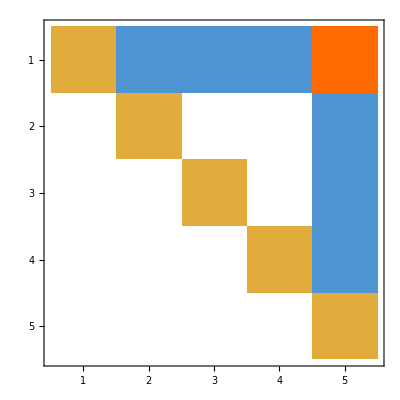

```mathematica
Inverse[ZetaM]//MatrixPlot
```

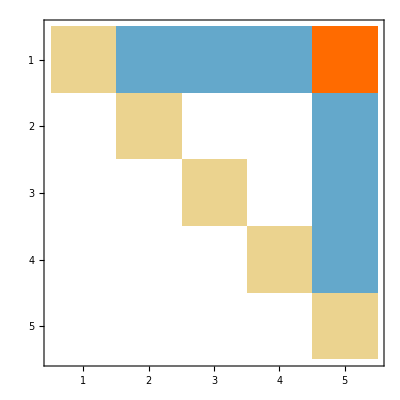

```mathematica
MatrixPower[Inverse[ZetaM],3]//MatrixPlot
```

```mathematica
MatrixPower[Inverse[ZetaM],15]//MatrixForm
```

(1 | -15 | -15 | -15 | 345
0 | 1 | 0 | 0 | -15
0 | 0 | 1 | 0 | -15
0 | 0 | 0 | 1 | -15
0 | 0 | 0 | 0 | 1)

```mathematica
Subgraph
```

Subgraph

```mathematica
GraphZeta[g_]:=Block[{ordered=TopologicalSort[four]},
Table[If[ToString[i]==ToString[j]||EdgeQ[g,i->j],1,0],{i,ordered},{j,ordered}]
]
```

```mathematica
GraphZeta[four]//MatrixForm
```

(1 | 1 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1)

```mathematica
Inverse[GraphZeta[four]]//MatrixForm
```

(1 | -1 | -1 | -1 | 3
0 | 1 | 0 | 0 | -1
0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 1)

```mathematica
MobiusTable[13]
```

<|2→{1},0→{2},1→{-1,-1,-1}|>